```mathematica
Eq1:=Df u''[z]==-Exp[-z/ℓ]/ℓ
```

```mathematica
Eq2 :=u[0] == ze u'[0]
```

```mathematica
Eq3 := u[L] ==-ze u'[L]
```

```mathematica
usol = u[z]/.DSolve[{Eq1, Eq2, Eq3},u[z],z][[1]]
```

1/(Df (L+2 ze))ⅇ^(-L/ℓ-z/ℓ) (ⅇ^(L/ℓ+z/ℓ) L ze-ⅇ^(L/ℓ+z/ℓ) z ze-ⅇ^(z/ℓ) z ze+ⅇ^(L/ℓ+z/ℓ) ze^2-ⅇ^(z/ℓ) ze^2+ⅇ^(L/ℓ+z/ℓ) L ℓ-ⅇ^(L/ℓ) L ℓ-ⅇ^(L/ℓ+z/ℓ) z ℓ+ⅇ^(z/ℓ) z ℓ+ⅇ^(L/ℓ+z/ℓ) ze ℓ-2 ⅇ^(L/ℓ) ze ℓ+ⅇ^(z/ℓ) ze ℓ)

```mathematica
FullSimplify[usol]
```

1/(Df (L+2 ze))ⅇ^(-(L+z)/ℓ) (-ⅇ^(L/ℓ) (L+2 ze) ℓ+ⅇ^(z/ℓ) (z+ze) (-ze+ℓ)+ⅇ^((L+z)/ℓ) (L-z+ze) (ze+ℓ))

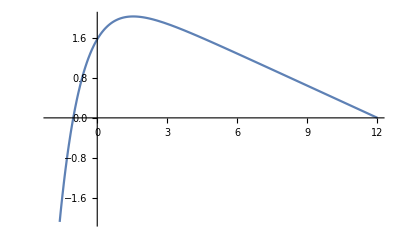

```mathematica
Plot[(usol/.{ℓ-> 1,ze->2,L->10, Df->1}), {z,-2,12}]
```

```mathematica
Series[usol,{ℓ,0,1}]
```

ⅇ^(ze/ℓ+O[ℓ]^2) (-(L ℓ)/(Df (L+2 ze))+O[ℓ]^2)+ⅇ^(-z/ℓ+O[ℓ]^2) ((L ℓ)/(Df (L+2 ze))+O[ℓ]^2)+ⅇ^((-L-ze)/ℓ+O[ℓ]^2) (-(z ℓ)/(Df (L+2 ze))+O[ℓ]^2)+ⅇ^(ze/ℓ+O[ℓ]^2) ((z ℓ)/(Df (L+2 ze))+O[ℓ]^2)+ⅇ^((-L-ze)/ℓ+O[ℓ]^2) (-(ze ℓ)/(Df (L+2 ze))+O[ℓ]^2)+ⅇ^(ze/ℓ+O[ℓ]^2) (-(ze ℓ)/(Df (L+2 ze))+O[ℓ]^2)+ⅇ^(-z/ℓ+O[ℓ]^2) ((2 ze ℓ)/(Df (L+2 ze))+O[ℓ]^2)